## angle>0 means >45 degrees inc. on PBS interface thingy a=between last 2 cubes b= reflected port of last cube c = transmitted port of last cube

```mathematica
angle={92,94.5,84,104,96,74,64,89}-84;
a={4.53,3.98,2.6,4.31,3.63,2.96,4.65};
b={.224,.239,.216,.13,.225,.181,.15,.235};
c={4.03,4.14,3.7,2.45,4.03,3.33,2.76,4.29};
```

## normal cubes. a could be unreliable b/c the second cube was changign the position of the beam on the power meter. Can use the sum of c and d to check. Also, at large cube angles, the detection cube is no longer normal...

```mathematica
angle={85,90,95,100,105,110,108,94.5,89,80,75,70,82,82,84,68,78,76,74}-85;
a={4.35,4.75,4.78,2.72,2.78,3.04,4.43,4.51,4.65,4.05,3.93,1.88,4.23,3.9,4.27,3.43,4,3.74,3.55};
c={4.02,4.4,4.45,2.6,2.68,2.87,4.32,4.23,4.3,3.7,3.38,3.22,3.92,3.65,3.95,3.25,3.71,3.48,3.4};
d={21,23,24,13,12,15.4,22,21,22,11,25,12,19,21,24,10,12,20,11}/1000;
b={405,73,54,1900,2100,1800,8.7,21,10.8,600,950,1200,590,550,520,1500,750,860,970}/1000;
```

## check that the max and min transmission sum up to a). concl: the -15 deg. incidence. the beam must be clipping on the power meter to be less than the sum, for the a) value.

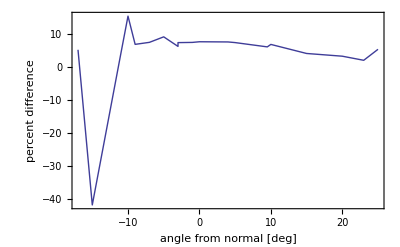

```mathematica
ListPlot[Sort[Thread[{angle,100 (a-(c+d))/(c+d)}]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"angle from normal [deg]","percent difference"}]
```

## as a function of angle, plot the total and percent power reflected by the cube to see the minima in relflection.. concl: 3 minima, at 4,9,and 25 deg.

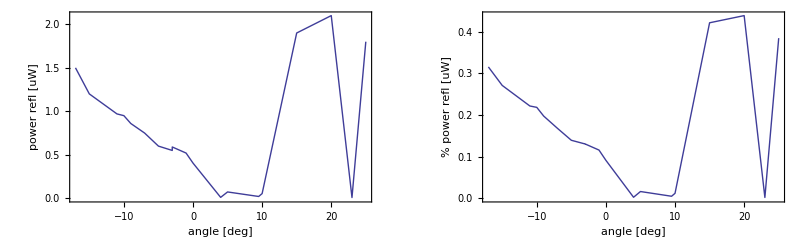

```mathematica
GraphicsGrid[{{ListPlot[Sort@Thread[{angle, b}],Joined->True,Axes->False,Frame->True,FrameLabel->{"angle [deg]","power refl [uW]"}],
ListPlot[Sort@Thread[{angle, b/(b+c+d)}],Joined->True,Axes->False,Frame->True,FrameLabel->{"angle [deg]","% power refl [uW]"}]}}]
```

## look at extinction as a fn of angle.

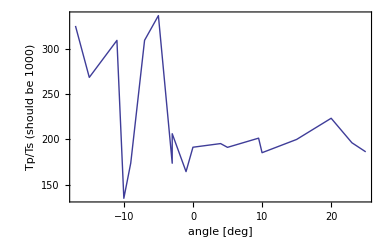

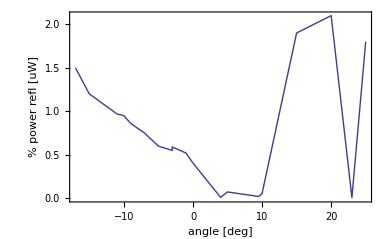

```mathematica
ListPlot[Sort@Thread[{angle, c/d}],Joined->True,Axes->False,Frame->True,FrameLabel->{"angle [deg]"," Tp/Ts (should be 1000)"},PlotRange->All]
ListPlot[Sort@Thread[{angle,b}],Joined->True,Axes->False,Frame->True,FrameLabel->{"angle [deg]","% power refl [uW]"}]
```